## Tephigram.

Let us begin with the definitions and notations of the various variables:

pressure			: p (in Pascals (Pa))
density				: ρ (kg/m^3)
temperature			: T (Kelvin (K))
Water-vapor mass fraction	: y = ρ_v/ρ
Relative humidity		: rh = p_v/P(T)
Saturated vapor pressure	: vp

Subscripts used:
			
ambient			: amb
moist adiabat			: moist
eye				: eye
tropopause			: trop
saturated			: sat
water vapor			: v
lifting condensation level	: switch
ocean-surface value		: s
underrunning moist air		: underrun.
Tropopause			: trop

Derived Subscripts used:

staturated water vapor		: vsat
amibent ocean-surface value	: ambs
water vapor ambient		: vamb

For the purposes of generating functions and code, we will not directly make use of subscripts but rather CAPITAL letters to indicate the subscripts. So, for example, rhAMB refers to ambient relative-humidity etc.


Constants:

gravity				: g (m/s^2)
gas constant for air		: R (m^2/s^2K)
Molecular weights ratio	: σ
Specific heat capacity 		: C_p (m^2/s^2K) (at constant pressure).
Specific latent heat		: L (m^2/s^2) (phase transition)
Temperature at 0^o C in K	: T_0=273.16 K.

Let us now define the various constants. The units are taken to be in SI units.

```mathematica
Clear["Global`*"];
g = 9.81;
R = 287.1;
σ = 0.622;
cp = 1004;
L = 2.5 10^6;
T0 = 273.16;

pAMBS = 101500.0;
tAMBS = 299.0;

performIterations = True;
```

Using equation of state, we can obtain the density at the ocean surface level:

```mathematica
ρAMBS = pAMBS/(R*tAMBS)
```

1.18239

We now obtain relative humidity as a function of pressure (rh_AMB(p)) and ambient temperature as a function of pressure (T_AMB(p)) from discrete tabulated data. This data is interpolated to produce a continuous function that will be used for further computations:

```mathematica
rhAMB=Interpolation[{{101500,0.84},{100000,0.81},{95000,0.81},{90000,0.79},{85000,0.74},{80000,0.70},{75000,0.64},{70000,0.60},{65000,0.56},{60000,0.54},{55000,0.51},{50000,0.49},{45000,0.45},{40000,0.44},{30000,0.39},{20000,0.37},{10000,0.35}},InterpolationOrder->1];

tAMB=Interpolation[{{101500,299},{100000,299},{95000,296},{90000,293},{85000,290},{80000,288},{75000,285},{70000,282},{65000,278},{60000,274},{55000,271},{50000,266},{45000,261},{40000,255},{30000,240},{20000,218},{10000,210}},Method->"Spline"];
```

The saturated vapor pressure is computed using the following empirical formula:

p_V_SAT= 610.78 e^(a(T)(T-T_0)/(T-b(T))),
a(T) = If[T > T_0, 17.2693882, 21.8745584],
b(T) = If[T > T_0, 35.86, 7.66].

These values are obtained by performing a curvefit to data.

```mathematica
a[t_]:=If[t>T0,17.2693882,21.8745584];
b[t_]:=If[t>T0,35.86,7.66];
pVSAT[t_] = 610.78*Exp[a[t]*(t-T0)/(t-b[t])];
dpVSAT[t_] := (pVSAT[t])*(a[t])*(T0-b[t])/(t-b[t])^2;
```

#### AMBIENT PROFILES:

The ambient profiles with altitudes can be computed using equation of state:
p = ρ R T → ρ = p/(RT), 
ρ p_v= ρ_vR T → p_v= y R T,
y = ρ_v/ρ.

```mathematica
ρAMB[p_]:= p/(R*tAMB[p]);
pVAMB[p_] := rhAMB[p]*pVSAT[tAMB[p]];
ρVAMB[p_]:=σ*pVAMB[p]/(R*tAMB[p]);
yAMB[p_] := ρVAMB[p]/ρAMB[p];
```

From the hydrostatic principles, using the relation (∂P)/(∂z)=-ρ g, we can compute the altitude (z) for the ambient case. The initial condition is z(P_ambs) =0. :

```mathematica
Remove[zAMB];
zAMB[p_?NumericQ]= NDSolveValue[{D[zAMB[p],p]==-1/(g*ρAMB[p]),zAMB[pAMBS]==0},zAMB[p],{p,pAMBS,10000},MaxStepSize->100,StartingStepSize->100];
```

#### MOIST ADIABAT PROFILES:

We now consider the moist adiabat profiles. We start with the thermodynamic relations between remperature and pressure:

γ = 1.4,

(T/T_ref)^(γ/(γ-1))=p/p_ref=p_v/p_v_ref, on a dry adiabat (since water vapor mass fraction (y) is constant).

Let T be the lifting-condensation level (LCL) state and left T_ref be the sea-level ambient state. 

(((T_sat)_onset)/T_ambs)^3.5=(p_vsat((T_sat)_onset))/(rh_ambs(p_ambs)p_vsat(T_ambs)).

The Temperature (T_sat)_onset can be computed using a root-finder. This gives the temperature at which the surface air would saturate if lifted dry adiabatically. The temperature implies a certain pressure on the adiabat and can be computed from the above equations.

```mathematica
tSWITCH=Block[{t},t/.FindRoot[pVSAT[t]/((t/tAMBS)^3.5)==(rhAMB[pAMBS])*(pVSAT[tAMBS]),{t,315,200}]];
pSWITCH = pAMBS*(tSWITCH/tAMBS)^3.5 ;
Print[StringForm["pLCL = `` [Pa], TLCL = `` [K]",Sequence@@(StandardForm/@{pSWITCH,tSWITCH})]]
```

pLCL = 97269.5 [Pa], TLCL = 295.385 [K]

Once saturated, the moist adiabat follows the following locus of the thrmodynamic states to rough approximation (the condensate falls out):

c_p dT + L σ d(p_vsat(T)/p) - dp/ρ = 0,
c_p dT/dp + L σ (d(p_vsat/p))/dp - RT/p = 0,
c_p dT/dp + (Lσ/p^2) (dp_vsat/dT dT/dp p-p_vsat)- RT/p = 0,
(c_p+(Lσ/p)dp_vsat/dT)dT/dp - (Lσ/p^2)p_vsat - RT/p=0.

and T(p_onset) = (T_sat)_onset

```mathematica
ClearSystemCache[];
{temp,val}=Reap[NDSolveValue[{(cp + (L*σ/p)*dpVSAT[tmoist1[p]])*D[tmoist1[p],p] - (L*σ*pVSAT[tmoist1[p]]/p^2) - R*tmoist1[p]/p == 0,tmoist1[pSWITCH]==tSWITCH, WhenEvent[tmoist1[p]==tAMB[p],Sow[p]]},tmoist1[p],{p,pSWITCH,10000}]]
```

{InterpolatingFunction[{{10000., 97269.5}}, <>][p],{{88328.,18843.1}}}

```mathematica
Rasterize[Plot[{temp,tAMB[p]},{p,pSWITCH,10000}, PlotStyle->{Red,Directive[Blue,Dashed]}, Axes->False, Frame->True,FrameLabel->{{"P (Pa)",""}, {"T(K)","Temperature Vs Pressure for Ambient"}}, FrameStyle->Directive[Black,14], ImageSize->500, PlotLegends->{"Moist adiabat","Ambient"}]]
```

-Graphics-

We can see that the ambient temperature crosses the moist adiabat temperature at two locations. However, we are more interested in the crossing between the ambient and the moist adiabat temperature at the higher alititude, i.e. at the lower pressure. The location of the crossing is known as the TROPOPAUSE. The pressure at the tropopause is is therefore taken as the lower value:

```mathematica
pTROP = val[[1,2]]
```

18843.1

Once the pressure at the tropopause is known, the temperature and density can be computed using the ambient relationships derived earlier. The height of the tropopause can also be computed from the altitude (z) function derived earlier.

```mathematica
tTROP=tAMB[pTROP];
zTROP=zAMB[pTROP];
ρTROP=ρAMB[pTROP];

Print[StringForm["\n zTROP = `` [m], pTROP = `` [Pa], tTROP = `` [K], ρTROP = `` [kg/m^3]",Sequence@@(StandardForm/@{zTROP,pTROP,tTROP,ρTROP})]]
```

zTROP = 12727.8 [m], pTROP = 18843.1 [Pa], tTROP = 215.816 [K], ρTROP = 0.304112 [kg/m^3]

We now note that the moist-adiabat locus is based on the total energy (c_p T + Ly + gz + q^2/2 = Const.), where q^2/2 is the kinetic energy and is about 1.5% of the contribution to the total. Therefore the KE is discarded. 

Integrating from the tropopause seaward would now allow the computation of the thermodynamic states holding at the base z=0. The equation to be integrated are:

dp/dz=-ρg,
c_p dT/dz+σ L d/dZ((p_vsat(T))/p) - (1/ρ) dp/dz=0.

Since we will be integrating with respect to pressure, the equations are written as:

dz/dp = -(RT/pg),
c_p dT/dp+σ L d/dp((p_vsat(T))/p) - (RT/p) =0.

Now, we must also take into account that when pressure reaches the pressure at lifting condensation level (LCL), the terms associated with latent heat (L) drop out. In other words, when the pressure reaches the lifting condensation level, we have to switch over to dry-adiabat conditions. Taking this into account, the final form of the equations to be integrated are:

dz/dp = -(RT/pg),
(c_p+((H(p_LCL-p)Lσ)/p)dp_vsat/dT)dT/dp - ((L H(p_LCL-p)σ)/p^2)p_vsat - RT/p=0,

where H denotes the step function. However, rather than producing a discontinuous jump, an approximation of the unit step function is used to facilitate a smooth transition between the layers. The approximation used here is

H(x) ≈ 1/(1 + e^(-2 k x)) and k is a large number.  Here k = 500.

The intial conditions for altitude (z) and temperature (T) are taken to be the values at the tropopause.

```mathematica
Remove[h,zMOIST,tMOIST,temp];
h[x_]:= 1/(1+Exp[-2*1000*x]);
temp = NDSolveValue[{D[zMOIST[p],p]==-(R tMOIST[p])/(p g),
(cp + (L*σ*h[pSWITCH-p]/p)*D[pVSAT[tMOIST[p]],tMOIST[p]])*D[tMOIST[p],p] - (L*σ*h[pSWITCH-p]/p^2)*pVSAT[tMOIST[p]] - R*tMOIST[p]/p == 0,
zMOIST[pTROP] == zTROP, tMOIST[pTROP]==tTROP},{zMOIST[p],tMOIST[p]},{p,pTROP,pAMBS}, MaxStepSize->100,StartingStepSize->100,AccuracyGoal->Infinity];
zMOIST[p_?NumericQ] = temp[[1]];
tMOIST[p_?NumericQ] = temp[[2]];
```

The value of the moist adiabat pressure at the surface z=0 (and therefore the temperature) can now be computed as:

```mathematica
pMOISTS = Block[{p}, p /. FindRoot[zMOIST[p]==0,{p,pAMBS}]];
tMOISTS = tMOIST[pMOISTS];

Print[StringForm["\n pMOIST at surface pMOISTS = `` [Pa], tMOIST at surface tMOISTS = `` [K]",Sequence@@(StandardForm/@{pMOISTS,tMOISTS})]]
```

pMOIST at surface pMOISTS = 99871.3 [Pa], tMOIST at surface tMOISTS = 297.623 [K]

This  pressure and from it the temperature and pressure should be used as the next iterate to refine the results. We need to do this because we started with an assumption on the values of the pressure and temperature at the sea-level. However, these values are typically not relevant to a vertical column in the core. 

To this end, we now set up an iteration scheme to test the convergence (or divergence) of the system. The iteration scheme is set so that the average relative error between the ambient pressure and temperature at ocean surface is less than 10^-5.

```mathematica
If[performIterations,
Print["................... starting iterations....................."];
Do[
ρMOISTS = pMOISTS/(R*tMOISTS);

Print[StringForm["pMOISTS = `` [Pa], tMOISTS = `` [K], ρMOISTS = `` [kg/m^3]", Sequence@@(StandardForm/@{pMOISTS,tMOISTS,ρMOISTS})]];

tSWITCH=Block[{t},t/.FindRoot[pVSAT[t]/((t/tMOISTS)^3.5)==(rhAMB[pMOISTS])*(pVSAT[tMOISTS]),{t,315,200}]];
pSWITCH = pMOISTS*(tSWITCH/tMOISTS)^3.5 ;
Print[StringForm["pLCL = `` [Pa], TLCL = `` [K]",Sequence@@(StandardForm/@{pSWITCH,tSWITCH})]];

Clear[tmoist1];
tmoist1[p_?NumericQ]=NDSolveValue[{(cp + (L*σ/p)*dpVSAT[tmoist1[p]])*D[tmoist1[p],p] - (L*σ*pVSAT[tmoist1[p]]/p^2) - R*tmoist1[p]/p == 0,tmoist1[pSWITCH]==tSWITCH},tmoist1[p],{p,pSWITCH,10000},MaxStepSize->100, StartingStepSize->100];

pTROP=Block[{p},p/.FindRoot[(tmoist1[p])-tAMB[p]==0,{p,10000,50000}]];
tTROP=tAMB[pTROP];
zTROP=zAMB[pTROP];
ρTROP=ρAMB[pTROP];

Print[StringForm["zTROP = `` [m], pTROP = `` [Pa], tTROP = `` [K], ρTROP = `` [kg/m^3]",Sequence@@(StandardForm/@{zTROP,pTROP,tTROP,ρTROP})]];

Clear[zMOIST,tMOIST];
temp = NDSolveValue[{D[zMOIST[p],p]==-(R tMOIST[p])/(p g),
(cp + (L*σ*h[pSWITCH-p]/p)*dpVSAT[tMOIST[p]])*D[tMOIST[p],p] - (L*σ*h[pSWITCH-p]/p^2)*pVSAT[tMOIST[p]] - R*tMOIST[p]/p == 0,
zMOIST[pTROP] == zTROP, tMOIST[pTROP]==tTROP},{zMOIST[p],tMOIST[p]},{p,pTROP,pAMBS}, MaxStepSize->100,StartingStepSize->100,AccuracyGoal->Infinity];

zMOIST[p_?NumericQ] = temp[[1]];
tMOIST[p_?NumericQ] = temp[[2]];

pMOISTSNew = Block[{p},p/.Quiet@FindRoot[zMOIST[p]==0,{p,pMOISTS}]];
tMOISTSNew = tMOIST[pMOISTSNew];

avgRelativeError = (Abs[(pMOISTS-pMOISTSNew)/pMOISTS]+ Abs[(tMOISTS-tMOISTSNew)/tMOISTS])/2;
Print["average err ->", avgRelativeError];

If[avgRelativeError < 10^-5, Break[]];

Print["err pAMBS->",Abs[(pMOISTS-pMOISTSNew)/pMOISTS]];
Print["err tAMBS ->", Abs[(tMOISTS-tMOISTSNew)/tMOISTS]]; 

pMOISTS = pMOISTSNew;
tMOISTS = tMOISTSNew;
ρMOISTS = pMOISTS/(R*tMOISTS);

Print[StringForm["............... iteration ->  `1` done....................", iter]];
,{iter,30}
];

Print["final result -->"];
Print[StringForm["pMOISTS = `` [Pa], tMOISTS = `` [K], ρMOISTS = `` [kg/m^3]", Sequence@@(StandardForm/@{pMOISTS,tMOISTS,ρMOISTS})]];
];
```

................... starting iterations.....................

pMOISTS = 99871.3 [Pa], tMOISTS = 297.623 [K], ρMOISTS = 1.1688 [kg/m^3]

pLCL = 94907.4 [Pa], TLCL = 293.319 [K]

zTROP = 11752.1 [m], pTROP = 21944.8 [Pa], tTROP = 222.071 [K], ρTROP = 0.344198 [kg/m^3]

average err ->0.00738885

err pAMBS->0.0114924

err tAMBS ->0.0032853

............... iteration ->  1 done....................

pMOISTS = 101019. [Pa], tMOISTS = 298.601 [K], ρMOISTS = 1.17836 [kg/m^3]

pLCL = 96548.7 [Pa], TLCL = 294.764 [K]

zTROP = 12491.7 [m], pTROP = 19558.3 [Pa], tTROP = 217.142 [K], ρTROP = 0.31373 [kg/m^3]

average err ->0.00499055

err pAMBS->0.00776527

err tAMBS ->0.00221583

............... iteration ->  2 done....................

pMOISTS = 100235. [Pa], tMOISTS = 297.939 [K], ρMOISTS = 1.17181 [kg/m^3]

pLCL = 95376.5 [Pa], TLCL = 293.74 [K]

zTROP = 12013. [m], pTROP = 21077.9 [Pa], tTROP = 220.204 [K], ρTROP = 0.333402 [kg/m^3]

average err ->0.0036278

err pAMBS->0.00563533

err tAMBS ->0.00162027

............... iteration ->  3 done....................

pMOISTS = 100799. [Pa], tMOISTS = 298.422 [K], ρMOISTS = 1.17651 [kg/m^3]

pLCL = 96220. [Pa], TLCL = 294.484 [K]

zTROP = 12375.9 [m], pTROP = 19917.3 [Pa], tTROP = 217.837 [K], ρTROP = 0.318468 [kg/m^3]

average err ->0.00259641

err pAMBS->0.00404556

err tAMBS ->0.00114726

............... iteration ->  4 done....................

pMOISTS = 100392. [Pa], tMOISTS = 298.08 [K], ρMOISTS = 1.17309 [kg/m^3]

pLCL = 95610.7 [Pa], TLCL = 293.953 [K]

zTROP = 12128.4 [m], pTROP = 20703. [Pa], tTROP = 219.421 [K], ρTROP = 0.32864 [kg/m^3]

average err ->0.00187229

err pAMBS->0.00290341

err tAMBS ->0.000841168

............... iteration ->  5 done....................

pMOISTS = 100683. [Pa], tMOISTS = 298.33 [K], ρMOISTS = 1.17551 [kg/m^3]

pLCL = 96046. [Pa], TLCL = 294.338 [K]

zTROP = 12313.8 [m], pTROP = 20112.4 [Pa], tTROP = 218.223 [K], ρTROP = 0.321018 [kg/m^3]

average err ->0.00135309

err pAMBS->0.00211292

err tAMBS ->0.000593263

............... iteration ->  6 done....................

pMOISTS = 100470. [Pa], tMOISTS = 298.153 [K], ρMOISTS = 1.17372 [kg/m^3]

pLCL = 95728.1 [Pa], TLCL = 294.063 [K]

zTROP = 12185.8 [m], pTROP = 20518.8 [Pa], tTROP = 219.043 [K], ρTROP = 0.32628 [kg/m^3]

average err ->0.00096786

err pAMBS->0.00149636

err tAMBS ->0.000439364

............... iteration ->  7 done....................

pMOISTS = 100621. [Pa], tMOISTS = 298.284 [K], ρMOISTS = 1.17496 [kg/m^3]

pLCL = 95952.5 [Pa], TLCL = 294.263 [K]

zTROP = 12281.9 [m], pTROP = 20212.9 [Pa], tTROP = 218.424 [K], ρTROP = 0.322327 [kg/m^3]

average err ->0.000706951

err pAMBS->0.00110833

err tAMBS ->0.000305569

............... iteration ->  8 done....................

pMOISTS = 100509. [Pa], tMOISTS = 298.193 [K], ρMOISTS = 1.17402 [kg/m^3]

pLCL = 95785.9 [Pa], TLCL = 294.12 [K]

zTROP = 12216.1 [m], pTROP = 20422. [Pa], tTROP = 218.845 [K], ρTROP = 0.325032 [kg/m^3]

average err ->0.000499775

err pAMBS->0.00076828

err tAMBS ->0.00023127

............... iteration ->  9 done....................

pMOISTS = 100586. [Pa], tMOISTS = 298.262 [K], ρMOISTS = 1.17465 [kg/m^3]

pLCL = 95901.1 [Pa], TLCL = 294.225 [K]

zTROP = 12266.6 [m], pTROP = 20261.5 [Pa], tTROP = 218.521 [K], ρTROP = 0.322957 [kg/m^3]

average err ->0.00037101

err pAMBS->0.000585963

err tAMBS ->0.000156057

............... iteration ->  10 done....................

pMOISTS = 100528. [Pa], tMOISTS = 298.216 [K], ρMOISTS = 1.17414 [kg/m^3]

pLCL = 95813. [Pa], TLCL = 294.151 [K]

zTROP = 12233.1 [m], pTROP = 20367.8 [Pa], tTROP = 218.736 [K], ρTROP = 0.324333 [kg/m^3]

average err ->0.000256921

err pAMBS->0.000390566

err tAMBS ->0.000123276

............... iteration ->  11 done....................

pMOISTS = 100567. [Pa], tMOISTS = 298.252 [K], ρMOISTS = 1.17446 [kg/m^3]

pLCL = 95871.6 [Pa], TLCL = 294.206 [K]

zTROP = 12260. [m], pTROP = 20282.2 [Pa], tTROP = 218.563 [K], ρTROP = 0.323226 [kg/m^3]

average err ->0.000196289

err pAMBS->0.000314268

err tAMBS ->0.00007831

............... iteration ->  12 done....................

pMOISTS = 100535. [Pa], tMOISTS = 298.229 [K], ρMOISTS = 1.17418 [kg/m^3]

pLCL = 95824.3 [Pa], TLCL = 294.168 [K]

zTROP = 12243.4 [m], pTROP = 20335.1 [Pa], tTROP = 218.669 [K], ρTROP = 0.32391 [kg/m^3]

average err ->0.000130726

err pAMBS->0.000194289

err tAMBS ->0.0000671637

............... iteration ->  13 done....................

pMOISTS = 100555. [Pa], tMOISTS = 298.249 [K], ρMOISTS = 1.17433 [kg/m^3]

pLCL = 95853.4 [Pa], TLCL = 294.197 [K]

zTROP = 12258.1 [m], pTROP = 20288.3 [Pa], tTROP = 218.575 [K], ρTROP = 0.323304 [kg/m^3]

average err ->0.000105384

err pAMBS->0.000172912

err tAMBS ->0.0000378561

............... iteration ->  14 done....................

pMOISTS = 100537. [Pa], tMOISTS = 298.238 [K], ρMOISTS = 1.17417 [kg/m^3]

pLCL = 95827.3 [Pa], TLCL = 294.177 [K]

zTROP = 12250.2 [m], pTROP = 20313.4 [Pa], tTROP = 218.626 [K], ρTROP = 0.323629 [kg/m^3]

average err ->0.0000650495

err pAMBS->0.0000921719

err tAMBS ->0.0000379271

............... iteration ->  15 done....................

pMOISTS = 100547. [Pa], tMOISTS = 298.249 [K], ρMOISTS = 1.17424 [kg/m^3]

pLCL = 95841.1 [Pa], TLCL = 294.193 [K]

zTROP = 12258.6 [m], pTROP = 20286.7 [Pa], tTROP = 218.572 [K], ρTROP = 0.323284 [kg/m^3]

average err ->0.0000579798

err pAMBS->0.0000991867

err tAMBS ->0.0000167728

............... iteration ->  16 done....................

pMOISTS = 100537. [Pa], tMOISTS = 298.244 [K], ρMOISTS = 1.17414 [kg/m^3]

pLCL = 95826.1 [Pa], TLCL = 294.183 [K]

zTROP = 12255.3 [m], pTROP = 20297.3 [Pa], tTROP = 218.593 [K], ρTROP = 0.323422 [kg/m^3]

average err ->0.0000308458

err pAMBS->0.0000389436

err tAMBS ->0.0000227479

............... iteration ->  17 done....................

pMOISTS = 100541. [Pa], tMOISTS = 298.251 [K], ρMOISTS = 1.17416 [kg/m^3]

pLCL = 95831.8 [Pa], TLCL = 294.191 [K]

zTROP = 12260.4 [m], pTROP = 20281.1 [Pa], tTROP = 218.56 [K], ρTROP = 0.323211 [kg/m^3]

average err ->0.0000333602

err pAMBS->0.0000609014

err tAMBS ->5.81888×10^-6

............... iteration ->  18 done....................

pMOISTS = 100534. [Pa], tMOISTS = 298.249 [K], ρMOISTS = 1.17409 [kg/m^3]

pLCL = 95822.6 [Pa], TLCL = 294.187 [K]

zTROP = 12259.4 [m], pTROP = 20284.2 [Pa], tTROP = 218.567 [K], ρTROP = 0.323252 [kg/m^3]

average err ->0.0000130561

err pAMBS->0.000011277

err tAMBS ->0.0000148352

............... iteration ->  19 done....................

pMOISTS = 100536. [Pa], tMOISTS = 298.254 [K], ρMOISTS = 1.17409 [kg/m^3]

pLCL = 95824.2 [Pa], TLCL = 294.192 [K]

zTROP = 12262.8 [m], pTROP = 20273.4 [Pa], tTROP = 218.545 [K], ρTROP = 0.323111 [kg/m^3]

average err ->0.0000205098

err pAMBS->0.0000409297

err tAMBS ->8.98957×10^-8

............... iteration ->  20 done....................

pMOISTS = 100531. [Pa], tMOISTS = 298.254 [K], ρMOISTS = 1.17404 [kg/m^3]

pLCL = 95818. [Pa], TLCL = 294.189 [K]

zTROP = 12263. [m], pTROP = 20272.7 [Pa], tTROP = 218.544 [K], ρTROP = 0.323102 [kg/m^3]

average err ->6.94502×10^-6

final result -->

pMOISTS = 100531. [Pa], tMOISTS = 298.254 [K], ρMOISTS = 1.17404 [kg/m^3]

We would like to emphasize that the results of the pressure and temperature for the moist adiabat at the beginnning of the iterations were:

 pMOIST at surface pMOISTS = 99871.3 [Pa], tMOIST at surface tMOISTS = 297.623 [K]
 
 So, the initial approximation is already a pretty good one.

```mathematica
ρMOIST[p_]:= p/(R*tMOIST[p]);
rhMOIST[p_?NumericQ]:= If[p>pSWITCH,(p/pSWITCH)*(pVSAT[tSWITCH])/(pVSAT[tMOIST[p]]),1]
pVMOIST[p_] := rhMOIST[p]*pVSAT[tMOIST[p]];;
ρVMOIST[p_]:=σ*pVMOIST[p]/(R*tMOIST[p]);
yMOIST[p_] := ρVMOIST[p]/ρMOIST[p];
```

#### EYE ADIABAT PROFILES:

Let us assume that the underrun happens at a certain pressure, say, p = 80000.00 Pa. The following equations are integrated from the tropopause to the surface and the height at which the underrun is computed:

dz/dp = -(RT/pg),
c_p dT/dp+σ L RH d/dp((p_vsat(T))/p) - (RT/p) =0,
p(ztrop) = ptrop, T(ztrop) = Ttrop.

In the above system, we have a new term RH (relative humiidty) which takes on a value 0≤ RH ≤1. 

If RH=0, then the eye is totally dry. In this case, the pressure at sea-level is quite decremented from the ambient pressure at the surface. 
If RH=1, all the heating in the eyewall owing to condensation is revered in the eye owing to evaporation.

Let us look at the effect of relative humidity on the profiles:

```mathematica
Remove[zEYE,tEYE, temp,RH];
pRange = Subdivide[pTROP,pAMBS,30];
pfunRH = ParametricNDSolveValue[{D[zEYE[p],p]==-(R tEYE[p])/(p g),
(cp + (L*σ*RH/p)*dpVSAT[tEYE[p]])*D[tEYE[p],p] - (L*σ*RH/p^2)*pVSAT[tEYE[p]] - R*tEYE[p]/p == 0,
zEYE[pTROP] == zTROP, tEYE[pTROP]==tTROP, WhenEvent[zEYE[p]==0, Sow[p]]},{zEYE,tEYE},{p,pTROP,pMOISTS}, RH];

Show[ListLinePlot[Table[{rhi, Reap[pfunRH[rhi]][[2,1,1]]}, {rhi,0,0.99,0.01}], PlotStyle->Black],
Plot[pMOISTS,{rh,0,1}, PlotRange->{{0,1},{pTROP,pMOISTS}}, PlotStyle->Red], PlotRange->All, Axes->None, Frame->True, FrameLabel->{{ Style["P (z=0) Pa",14],""},{Style["R.H.",14],"Pressure at surface for different relative humidities"}},
FrameStyle->Directive[Black,14], ImageSize->500] // Rasterize
```

-Graphics-

The above figure shows the effect of relative humidity on pressure at z=0. The red line is the ambient pressure at surface. Now, let us assume that the underrun happens at a pressure of 80000 Pa and the relative humidity from the tropopause to the underruun is 0.65. For this case, the altitude and temperature can be computed as:

```mathematica
RHPlus = 0.65; RHMinus = 1.0;
```

```mathematica
ClearSystemCache[];
pUnderrun = 80000.0;
{zEYEp, tEYEp} = pfunRH[RHPlus] ;
{zUnderrunPlus, tUnderrunPlus} = {zEYEp[pUnderrun], tEYEp[pUnderrun]}
```

{1875.29,292.283}

The surface pressure at the eye is computed as:

```mathematica
Block[{p}, p /. FindRoot[zEYEp[p]==0,{p,pMOISTS}]]
```

99292.1

At the underrun, the pressure is continuous but the temperature (and as a consequence density) will be discontinuous. The total energy will also be continuous. Therefore we equate the energy at the underrun as follows:

C_p T_+ + σ L RH_+P(T_+)/p^* = C_p T_- + σ L RH_-P(T_-)/p^*,

where p^* is the pressure at the underrun.

```mathematica
Remove[tUnderrunMinus];
tUnderrunMinus  = tUnderrunMinus /. FindRoot[cp*tUnderrunPlus + L*σ*RHPlus*pVSAT[tUnderrunPlus]/pUnderrun == cp*tUnderrunMinus + σ*L*RHMinus*pVSAT[tUnderrunMinus]/pUnderrun,{tUnderrunMinus, tUnderrunPlus}]
```

287.829

Using the temperature at the underrun (T_-), we now integrate the moist adiabat equations to get the temperature profile from underrun height to the surface.

```mathematica
Remove[zEYE,tEYE, zEYEm, tEYEm];
temp = NDSolveValue[{D[zEYE[p],p]==-(R tEYE[p])/(p g),
(cp + (L*σ*h[pSWITCH-p]/p)*D[pVSAT[tEYE[p]],tEYE[p]])*D[tEYE[p],p] - (L*σ*h[pSWITCH-p]/p^2)*pVSAT[tEYE[p]] - R*tEYE[p]/p == 0,
zEYE[pUnderrun] == zEYEp[pUnderrun], tEYE[pUnderrun]==tUnderrunMinus},{zEYE[p],tEYE[p]},{p,pUnderrun,pMOISTS}, MaxStepSize->100,StartingStepSize->100,AccuracyGoal->Infinity];
zEYEm[p_?NumericQ] = temp[[1]];
tEYEm[p_?NumericQ] = temp[[2]];
```

The final profiles will be a composite profile:

```mathematica
Remove[tEYE,zEYE];
tEYE[p_?NumericQ]:=If[p<pUnderrun,tEYEp[p],tEYEm[p]];
zEYE[p_?NumericQ]:=If[p<pUnderrun,zEYEp[p],zEYEm[p]];
rhEYE[p_?NumericQ]:= If[p<pUnderrun,RHPlus, RHMinus];

yEYEp[p_]:= RHPlus*σ*pVSAT[tEYEp[p]]/p;
yEYEm[p_]:= If[p <pSWITCH, σ*pVSAT[tEYEm[p]]/p, σ*pVSAT[tSWITCH]/pSWITCH];
yEYE[p_]:= If[p < pUnderrun, yEYEp[p], yEYEm[p]];

ρEYE[p_]:= p/(R*tEYE[p]);
```

```mathematica
ParametricPlot[{tEYE[p],p},{p,pAMBS,pTROP},Axes->None,Frame->True,FrameStyle->Directive[Black,14],FrameLabel->{"Teye (K)","P (Pa)"},PlotRange->All,AspectRatio->1,ScalingFunctions->{Identity,"Reverse"}, AxesOrigin->{200,10000}, PlotStyle->{Red,Dashed}, AxesStyle->Directive[Black,14],ImageSize->500, PlotLabel->Text@Style["Temperature in the eye at relative humidity = 0.65 and \n \t     underrun pressure = 800 hPa",Black,14]] // Rasterize
```

-Graphics-

```mathematica
ParametricPlot[{zEYE[p],tEYE[p]},{p,pTROP,pAMBS},Axes->None, Frame->True, FrameStyle->Directive[Black,14],FrameLabel->{"z (m)","Teye [K]"},PlotRange->All,AspectRatio->1,AxesOrigin->{0,200}, PlotStyle->{{Red,Dashed}},
PlotLabel->Text@Style["Temperature in the eye at relative humidity = 0.65 and \n \t     underrun pressure = 800 hPa",Black,14], ImageSize->500] // Rasterize
```

-Graphics-

#### The Composite Model:

```mathematica
Remove[zEYE,tEYE,yEYE, ρEYE,rhEYE,pz0, EyeAdiabat];
EyeAdiabat[pUnderrun_,rhplus_,rhminus_]:= Module[{ρEYE, zEYE, tEYE, yEYE, rhEYE, p, temp, if, pz0, switch, InterfaceTemperature},
InterfaceTemperature[p_?NumericQ, tplus_?NumericQ,rhp_?NumericQ,rhm_?NumericQ]:= Module[{tminus,res},
res = tminus /. FindRoot[cp*tplus + L*σ*rhp*pVSAT[tplus]/p == cp*tminus + σ*L*rhm*pVSAT[tminus]/p,{tminus, tplus}];
res
];
{zEYE,tEYE} = NDSolveValue[{D[zEYE[p],p]==-(R tEYE[p])/(p g),
(cp + (L*σ*(switch[p]*rhplus + (1-switch[p])*h[pSWITCH-p])/p)*dpVSAT[tEYE[p]])*D[tEYE[p],p] - (L*σ*(switch[p]*rhplus + (1-switch[p])*h[pSWITCH-p])/p^2)*pVSAT[tEYE[p]] - R*tEYE[p]/p == 0,
zEYE[pTROP] == zTROP, tEYE[pTROP]==tTROP, switch[pTROP]==1,
WhenEvent[p==pUnderrun, {tEYE[p]-> InterfaceTemperature[p, tEYE[p], rhplus,rhminus], switch[p]->0}],
WhenEvent[zEYE[p]==0, "StopIntegration"]},{zEYE,tEYE},{p,pTROP,Infinity}, DiscreteVariables->{switch ∈ {0,1}}];

pz0 = Last[Flatten@zEYE["Domain"]];
ρEYE = Function@@List[p, p/(R*tEYE[p])];

temp = if[p <pSWITCH, rhminus*σ*pVSAT[tEYE[p]]/p, σ*pVSAT[tSWITCH]/pSWITCH];
yEYE = Function@@List[p, (if[p < pUnderrun,  rhplus*σ*pVSAT[tEYE[p]]/p,temp])/. {if :>  If}];
rhEYE = Function@@List[p, If[p < pUnderrun, rhplus, rhminus]];
{pz0, zEYE,tEYE,ρEYE,yEYE, rhEYE}
];
```

```mathematica
{pz0, zEYE,tEYE,ρEYE,yEYE, rhEYE} = EyeAdiabat[80000,0.65,1];

ParametricPlot[{tEYE[p],p},{p,pz0,pTROP},Axes->None,Frame->True,FrameStyle->Directive[Black,14],FrameLabel->{"Teye (K)","P (Pa)"},PlotRange->All,AspectRatio->1,ScalingFunctions->{Identity,"Reverse"}, AxesOrigin->{200,10000}, PlotStyle->{Red,Dashed}, AxesStyle->Directive[Black,14],ImageSize->500, PlotLabel->Text@Style["Temperature in the eye at relative humidity = 0.65 and \n \t     underrun pressure = 800 hPa",Black,14]] // Rasterize
```

-Graphics-

```mathematica
{pz0, zEYE,tEYE,ρEYE,yEYE, rhEYE} = EyeAdiabat[10^15,0.0,1];

ParametricPlot[{tEYE[p],p},{p,pz0,pTROP},Axes->None,Frame->True,FrameStyle->Directive[Black,14],FrameLabel->{"Teye (K)","P (Pa)"},PlotRange->All,AspectRatio->1,ScalingFunctions->{Identity,"Reverse"}, AxesOrigin->{200,10000}, PlotStyle->{Red,Dashed}, AxesStyle->Directive[Black,14],ImageSize->500, PlotLabel->Text@Style["Temperature in the eye at relative humidity = 0.0 and no underrun",Black,14]] // Rasterize
```

-Graphics-

```mathematica
rhdata = Table[{{ri,purun},Quiet@First[EyeAdiabat[purun,ri,1]]},{ri,0.,0.99,0.01},{purun,0,100000,5000}];
rhinterp = Interpolation[Flatten[rhdata,1]];
```

```mathematica
Quiet@ContourPlot[rhinterp[rh, punderrun],{rh,0,1},{punderrun,0,100000}, Contours->20,ContourLabels->(Text[#3/1000.,{#1,#2},Background->White]&), ImageSize->600,FrameLabel->{Text[Style["RH",Black, 14]],Text@Style["   P_underrun(Pa)",Black,14]}
, PlotLabel->Text@Style["Pressure at surface (in hPa)",Black, 16]]
```

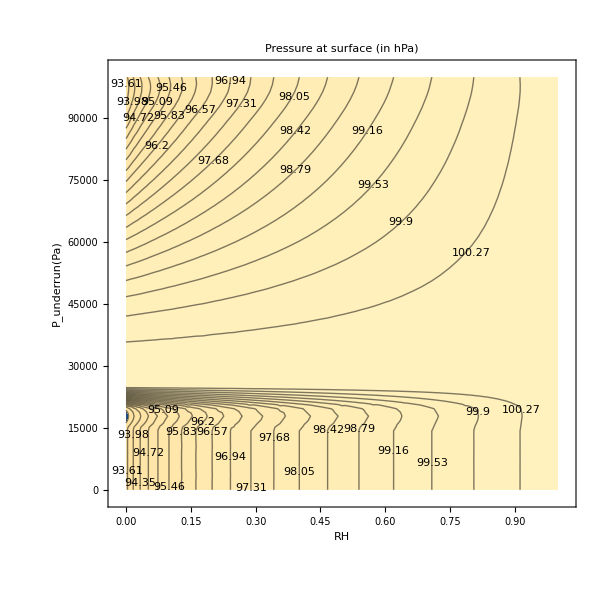
```mathematica
-Graphics- // Rasterize
```

-Graphics-

```mathematica
p1 = Show[Block[{c=0},Table[c+=0.1;Plot[rhinterp[rh,pi],{rh,0,1}, PlotStyle->Hue[c]],{pi,0,80000,10000}]], PlotRange->All, Axes->None, Frame->True, FrameStyle->Directive[Black,14], ImageSize->500, FrameLabel->{Text@Style["Relative humidity",16],Text@Style["Pressure (z=0)",16]} ];
p2 = Block[{c=0},ListLinePlot[{},PlotLegends->LineLegend[Sequence@@Transpose[Table[c+=0.1; {Hue[c],StringForm["`1` Pa",pi]},{pi,0,80000,10000}]], LegendLabel->"Underrun pressure \n", LabelStyle->14, LegendFunction->Framed]
]];
Show[p1,p2] // Rasterize
```

-Graphics-

```mathematica
{pz0, zEYE,tEYE,ρEYE,yEYE, rhEYE} = EyeAdiabat[80000,0.65,1];

Remove[totTempAMB, totTempMOIST, totTempEYE];
totTempAMB[p_?NumericQ]:=tAMB[p]+(g*zAMB[p]/cp)+(L*yAMB[p])/cp;
totTempMOIST[p_?NumericQ]:=tMOIST[p]+(g*zMOIST[p]/cp)+(L*yMOIST[p])/cp;
totTempEYE[p_?NumericQ]:=tEYE[p]+(g*zEYE[p]/cp)+(L*yEYE[p])/cp;

plotAMB=ParametricPlot[{totTempAMB[p],p},{p,pAMBS,pTROP},Axes->None, Frame->True, FrameStyle->Directive[Black,14],PlotRange->All,AspectRatio->1,AxesOrigin->{300,10000}, PlotStyle->{{Red,Dashed}},ScalingFunctions->{Identity,"Reverse"}];
plotMOIST=ParametricPlot[{totTempMOIST[p],p},{p,pAMBS,pTROP},PlotStyle->{{Blue,DotDashed}},ScalingFunctions->{Identity,"Reverse"}];
plotEYE=ParametricPlot[{totTempEYE[p],p},{p,pAMBS,pTROP},PlotStyle->Black,ScalingFunctions->{Identity,"Reverse"}];

Show[{plotAMB,plotMOIST,plotEYE,ListLinePlot[{},PlotLegends->LineLegend[{{Red,Dashed},{Blue,DotDashed},Black},{"ambient","moist-adiabat (Iterated)","eye"}]]},FrameLabel->{"T (K)","P (Pa)"},PlotLabel->Text@Style["Total Temperature Vs Pressure for ambient, eyewall, eye \n for relative humidity = 0.65 and underrunning at P = 800 hPa",Black, 16],FormatType->TraditionalForm,AxesOrigin->{300,10000},PlotRange->All,AspectRatio->1, ImageSize->500] // Rasterize
```

-Graphics-

```mathematica
{pz0, zEYE,tEYE,ρEYE,yEYE, rhEYE} = EyeAdiabat[10^15,0.0,1];

Remove[totTempAMB, totTempMOIST, totTempEYE];
totTempAMB[p_?NumericQ]:=tAMB[p]+(g*zAMB[p]/cp)+(L*yAMB[p])/cp;
totTempMOIST[p_?NumericQ]:=tMOIST[p]+(g*zMOIST[p]/cp)+(L*yMOIST[p])/cp;
totTempEYE[p_?NumericQ]:=tEYE[p]+(g*zEYE[p]/cp)+(L*yEYE[p])/cp;

plotAMB=ParametricPlot[{totTempAMB[p],p},{p,pAMBS,pTROP},Axes->None, Frame->True, FrameStyle->Directive[Black,14],PlotRange->All,AspectRatio->1,AxesOrigin->{300,10000}, PlotStyle->{{Red,Dashed}},ScalingFunctions->{Identity,"Reverse"}];
plotMOIST=ParametricPlot[{totTempMOIST[p],p},{p,pAMBS,pTROP},PlotStyle->{{Blue,DotDashed}},ScalingFunctions->{Identity,"Reverse"}];
plotEYE=ParametricPlot[{totTempEYE[p],p},{p,pAMBS,pTROP},PlotStyle->Black,ScalingFunctions->{Identity,"Reverse"}];

Show[{plotAMB,plotMOIST,plotEYE,ListLinePlot[{},PlotLegends->LineLegend[{{Red,Dashed},{Blue,DotDashed},Black},{"ambient","moist-adiabat (Iterated)","eye"}]]},FrameLabel->{"T (K)","P (Pa)"},PlotLabel->Text@Style["Total Temperature Vs Pressure for ambient, eyewall, eye \n       for relative humidity = 0 and no underrunning",Black, 16],FormatType->TraditionalForm,AxesOrigin->{300,10000},PlotRange->All,AspectRatio->1, ImageSize->500] // Rasterize
```

-Graphics-

```mathematica
{pz0, zEYE,tEYE,ρEYE,yEYE, rhEYE} = EyeAdiabat[80000,0.65,1];

plotAMB=ParametricPlot[{p, zAMB[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1, PlotStyle->{{Red,Dashed}}];
plotMOIST=ParametricPlot[{p, zMOIST[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1,PlotStyle->{{Blue,DotDashed}}];
plotEYE=ParametricPlot[{p,zEYE[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1,PlotStyle->Black];

pp = Show[{plotAMB,plotMOIST,plotEYE}, PlotRange->{{90000,110000},{-500,500}}, Axes->None,Frame->True, FrameStyle->Directive[Black,14],FrameTicks->{{{-500,0,500},None},{{90000,100000,110000},None}}, ImageSize->220];

Show[{plotAMB,plotMOIST,plotEYE,ListLinePlot[{},PlotLegends->LineLegend[{{Red,Dashed},{Blue,DotDashed},Black},{"ambient","moist adiabat (Iterated)","eye"}]]},PlotLabel->Text@Style["Altitude Vs Pressure, for ambient, moist-adiabat and eye \n for relative humifity = 0.65 and underrunning at P = 800 hPa",Black,16],
Axes->False, Frame->True, FrameStyle->Directive[Black,14], FrameLabel -> {"P (Pa)", "z (m)"},
FormatType->TraditionalForm,PlotRange->All,AspectRatio->1, ImageSize->500, Epilog->Inset[pp,{80000,8000}]] // Rasterize
```

-Graphics-

```mathematica
{pz0, zEYE,tEYE,ρEYE,yEYE, rhEYE} = EyeAdiabat[10^15,0.0,1];

plotAMB=ParametricPlot[{p, zAMB[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1, PlotStyle->{{Red,Dashed}}];
plotMOIST=ParametricPlot[{p, zMOIST[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1,PlotStyle->{{Blue,DotDashed}}];
plotEYE=ParametricPlot[{p,zEYE[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1,PlotStyle->Black];

pp = Show[{plotAMB,plotMOIST,plotEYE}, PlotRange->{{90000,110000},{-1000,500}}, Axes->None,Frame->True, FrameStyle->Directive[Black,14],FrameTicks->{{{-500,0,500},None},{{90000,100000,110000},None}}, ImageSize->220];

Show[{plotAMB,plotMOIST,plotEYE,ListLinePlot[{},PlotLegends->LineLegend[{{Red,Dashed},{Blue,DotDashed},Black},{"ambient","moist adiabat (Iterated)","eye (dry; no underruning)"}]]},PlotLabel->Text@Style["Altitude Vs Pressure, for ambient, moist-adiabat and eye \n \t    for dry eye and no underrunning",Black,16],
Axes->False, Frame->True, FrameStyle->Directive[Black,14], FrameLabel -> {"P (Pa)", "z (m)"},
FormatType->TraditionalForm,PlotRange->All,AspectRatio->1, ImageSize->500, Epilog->Inset[pp,{80000,8000}]] // Rasterize
```

-Graphics-

```mathematica
{pz0, zEYE,tEYE,ρEYE,yEYE, rhEYE} = EyeAdiabat[80000,0.65,1];

plotAMB=ParametricPlot[{rhAMB[p],p},{p,pAMBS,pTROP},AxesLabel->{"relative humidity","p [Pa]"},PlotRange->All,AspectRatio->1, PlotStyle->{{Red,Dashed}},ScalingFunctions->{Identity,"Reverse"}];
plotMOIST=ParametricPlot[{rhMOIST[p],p},{p,pAMBS,pTROP},AxesLabel->{"relative humidity","p [Pa]"},PlotRange->All,AspectRatio->1,PlotStyle->{{Blue,DotDashed}},ScalingFunctions->{Identity,"Reverse"}];
plotEYE=ParametricPlot[{rhEYE[p],p},{p,pAMBS,pTROP},AxesLabel->{"relative humidity","p [Pa]"},PlotRange->All,AspectRatio->1,PlotStyle->Black,ScalingFunctions->{Identity,"Reverse"}];

Show[{plotAMB,plotMOIST,plotEYE,ListLinePlot[{},PlotLegends->LineLegend[{{Red,Dashed},{Blue,DotDashed},Black},{"ambient","moist adiabat (Iterated)","eye"}]]},PlotLabel->Text@Style["Relative humidity Vs Pressure, for ambient, moist-adiabat and eye \n for relative humidity = 0.65 and underrunning at P = 800 hPa",Black,16],
Axes->False, Frame->True, FrameStyle->Directive[Black,14], FrameLabel -> {"RH", "P (Pa)"},
FormatType->TraditionalForm,PlotRange->All,AspectRatio->1, ImageSize->500] // Rasterize
```

-Graphics-

```mathematica
{pz0, zEYE,tEYE,ρEYE,yEYE, rhEYE} = EyeAdiabat[10^15,0.65,1];

plotAMB=ParametricPlot[{rhAMB[p],p},{p,pAMBS,pTROP},AxesLabel->{"relative humidity","p [Pa]"},PlotRange->All,AspectRatio->1, PlotStyle->{{Red,Dashed}},ScalingFunctions->{Identity,"Reverse"}];
plotMOIST=ParametricPlot[{rhMOIST[p],p},{p,pAMBS,pTROP},AxesLabel->{"relative humidity","p [Pa]"},PlotRange->All,AspectRatio->1,PlotStyle->{{Blue,DotDashed}},ScalingFunctions->{Identity,"Reverse"}];
plotEYE=ParametricPlot[{rhEYE[p],p},{p,pAMBS,pTROP},AxesLabel->{"relative humidity","p [Pa]"},PlotRange->All,AspectRatio->1,PlotStyle->Black,ScalingFunctions->{Identity,"Reverse"}];

Show[{plotAMB,plotMOIST,plotEYE,ListLinePlot[{},PlotLegends->LineLegend[{{Red,Dashed},{Blue,DotDashed},Black},{"ambient","moist adiabat (Iterated)","eye"}]]},PlotLabel->Text@Style["Relative humidity Vs Pressure, for ambient, moist-adiabat and eye \n    \t  for relative humidity = 0.65 and no underrunning",Black,16],
Axes->False, Frame->True, FrameStyle->Directive[Black,14], FrameLabel -> {"RH", "P (Pa)"},
FormatType->TraditionalForm,PlotRange->All,AspectRatio->1, ImageSize->500] // Rasterize
```

-Graphics-

```mathematica
{pz0, zEYE,tEYE,ρEYE,yEYE, rhEYE} = EyeAdiabat[10^15,0.0,1];

plotAMB=ParametricPlot[{rhAMB[p],p},{p,pAMBS,pTROP},AxesLabel->{"relative humidity","p [Pa]"},PlotRange->All,AspectRatio->1, PlotStyle->{{Red,Dashed}},ScalingFunctions->{Identity,"Reverse"}];
plotMOIST=ParametricPlot[{rhMOIST[p],p},{p,pAMBS,pTROP},AxesLabel->{"relative humidity","p [Pa]"},PlotRange->All,AspectRatio->1,PlotStyle->{{Blue,DotDashed}},ScalingFunctions->{Identity,"Reverse"}];
plotEYE=ParametricPlot[{rhEYE[p],p},{p,pAMBS,pTROP},AxesLabel->{"relative humidity","p [Pa]"},PlotRange->All,AspectRatio->1,PlotStyle->Black,ScalingFunctions->{Identity,"Reverse"}];

Show[{plotAMB,plotMOIST,plotEYE,ListLinePlot[{},PlotLegends->LineLegend[{{Red,Dashed},{Blue,DotDashed},Black},{"ambient","moist adiabat (Iterated)","eye (dry; no underrunning)"}]]},PlotLabel->Text@Style["Relative humidity Vs Pressure, for ambient, moist-adiabat and eye \n    \t  for dry eye and no underrunning",Black,16],
Axes->False, Frame->True, FrameStyle->Directive[Black,14], FrameLabel -> {"RH", "P (Pa)"},
FormatType->TraditionalForm,PlotRange->All,AspectRatio->1, ImageSize->500] // Rasterize
```

-Graphics-

```mathematica
{pz0, zEYE,tEYE,ρEYE,yEYE, rhEYE} = EyeAdiabat[80000,0.65,1];

plotAMB=ParametricPlot[{tAMB[p],p},{p,pAMBS,pTROP},AxesLabel->{"T [K]","p [Pa]"},PlotRange->All,AspectRatio->1, PlotStyle->{{Red,Dashed}},ScalingFunctions->{Identity,"Reverse"}];
plotMOIST=ParametricPlot[{tMOIST[p],p},{p,pAMBS,pTROP},AxesLabel->{"T [K]","p [Pa]"},PlotRange->All,AspectRatio->1,PlotStyle->{{Blue,DotDashed}},ScalingFunctions->{Identity,"Reverse"}];
plotEYE=ParametricPlot[{tEYE[p],p},{p,pAMBS,pTROP},AxesLabel->{"T [K]","p [Pa]"},PlotRange->All,AspectRatio->1,PlotStyle->Black,ScalingFunctions->{Identity,"Reverse"}];

pp = Show[{plotAMB,plotMOIST,plotEYE}, ScalingFunctions->{Identity,"Reverse"},PlotRange->{{298,300},{-102000,-100000}}, Axes->None, Frame->True, FrameTicks->{{{{-100000,100000},{-101000,101000},{-102000,102000}},None},{{297,298,299,300},None}}, ImageSize->180];

Show[{plotAMB,plotMOIST,plotEYE,ListLinePlot[{},PlotLegends->LineLegend[{{Red,Dashed},{Blue,DotDashed},Black},{"ambient","moist adiabat (Iterated)","eye"}]]},PlotLabel->Text@Style["Temperature Vs Pressure, for ambient, moist-adiabat and eye \n for relative humidity = 0.65 and underrunning at P = 800 hPa",Black,16],
Axes->False, Frame->True, FrameStyle->Directive[Black,14], FrameLabel -> {"T (K)", "P (Pa)"},
FormatType->TraditionalForm,PlotRange->All,AspectRatio->1, ImageSize->500, Epilog->Inset[pp,{245,-80000}]] // Rasterize
```

-Graphics-

```mathematica
{pz0, zEYE,tEYE,ρEYE,yEYE, rhEYE} = EyeAdiabat[10^15,0.0,1];

plotAMB=ParametricPlot[{tAMB[p],p},{p,pAMBS,pTROP},AxesLabel->{"T [K]","p [Pa]"},PlotRange->All,AspectRatio->1, PlotStyle->{{Red,Dashed}},ScalingFunctions->{Identity,"Reverse"}];
plotMOIST=ParametricPlot[{tMOIST[p],p},{p,pAMBS,pTROP},AxesLabel->{"T [K]","p [Pa]"},PlotRange->All,AspectRatio->1,PlotStyle->{{Blue,DotDashed}},ScalingFunctions->{Identity,"Reverse"}];
plotEYE=ParametricPlot[{tEYE[p],p},{p,pAMBS,pTROP},AxesLabel->{"T [K]","p [Pa]"},PlotRange->All,AspectRatio->1,PlotStyle->Black,ScalingFunctions->{Identity,"Reverse"}];

pp = Show[{plotAMB,plotMOIST,plotEYE}, ScalingFunctions->{Identity,"Reverse"},PlotRange->{{298,300},{-102000,-100000}}, Axes->None, Frame->True, FrameTicks->{{{{-100000,100000},{-101000,101000},{-102000,102000}},None},{{297,298,299,300},None}}, ImageSize->180];

Show[{plotAMB,plotMOIST,plotEYE,ListLinePlot[{},PlotLegends->LineLegend[{{Red,Dashed},{Blue,DotDashed},Black},{"ambient","moist adiabat (Iterated)","eye (dry; no underrunning)"}]]},PlotLabel->Text@Style["Temperature Vs Pressure, for ambient, moist-adiabat and eye \n         for relative humidity = 0.0 and no underrunning",Black,16],
Axes->False, Frame->True, FrameStyle->Directive[Black,14], FrameLabel -> {"T (K)", "P (Pa)"},
FormatType->TraditionalForm,PlotRange->All,AspectRatio->1, ImageSize->500, Epilog->Inset[pp,{245,-85000}]] // Rasterize
```

-Graphics-

```mathematica
{pz0, zEYE,tEYE,ρEYE,yEYE, rhEYE} = EyeAdiabat[80000,0.65,1];

plotAMB=ParametricPlot[{tAMB[p],zAMB[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1, PlotStyle->{{Red,Dashed}}];
plotMOIST=ParametricPlot[{tMOIST[p],zMOIST[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1,PlotStyle->{{Blue,DotDashed}}];
plotEYE=ParametricPlot[{tEYE[p],zEYE[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1,PlotStyle->Black];

pp = Show[{plotAMB,plotMOIST,plotEYE}, ScalingFunctions->{Identity,"Reverse"},PlotRange->{{292,301},{0,500}}, Axes->None, Frame->True];

Show[{plotAMB,plotMOIST,plotEYE,ListLinePlot[{},PlotLegends->LineLegend[{{Red,Dashed},{Blue,DotDashed},Black},{"ambient","moist adiabat (Iterated)","eye"}]]},PlotLabel->Text@Style["Temperature Vs Altitude, for ambient, moist-adiabat and eye \n for relative humidity = 0.65 and underrunning at P = 800 hPa",Black,16],
Axes->False, Frame->True, FrameStyle->Directive[Black,14], FrameLabel -> {"T (K)", "z (m)"},
FormatType->TraditionalForm,PlotRange->All,AspectRatio->1, ImageSize->500, Epilog->Inset[pp,{245,3000}]] // Rasterize
```

-Graphics-

```mathematica
{pz0, zEYE,tEYE,ρEYE,yEYE, rhEYE} = EyeAdiabat[10^15,0.0,1];

plotAMB=ParametricPlot[{tAMB[p],zAMB[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1, PlotStyle->{{Red,Dashed}}];
plotMOIST=ParametricPlot[{tMOIST[p],zMOIST[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1,PlotStyle->{{Blue,DotDashed}}];
plotEYE=ParametricPlot[{tEYE[p],zEYE[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1,PlotStyle->Black];

pp = Show[{plotAMB,plotMOIST,plotEYE}, ScalingFunctions->{Identity,"Reverse"},PlotRange->{{292,301},{0,500}}, Axes->None, Frame->True];

Show[{plotAMB,plotMOIST,plotEYE,ListLinePlot[{},PlotLegends->LineLegend[{{Red,Dashed},{Blue,DotDashed},Black},{"ambient","moist adiabat (Iterated)","eye (dry; no underrunning)"}]]},PlotLabel->Text@Style["Temperature Vs Altitude, for ambient, moist-adiabat and eye \n      for relative humidity = 0.0 and no underrunning",Black,16],
Axes->False, Frame->True, FrameStyle->Directive[Black,14], FrameLabel -> {"T (K)", "z (m)"},
FormatType->TraditionalForm,PlotRange->All,AspectRatio->1, ImageSize->500, Epilog->Inset[pp,{320,8000}]] // Rasterize
```

-Graphics-

```mathematica
{pz0, zEYE,tEYE,ρEYE,yEYE, rhEYE} = EyeAdiabat[80000,0.65,1];

plotAMB=ParametricPlot[{ρAMB[p],p},{p,pAMBS,pTROP},AxesLabel->{"Density [kg/m^3]","p [Pa]"},PlotRange->All,AspectRatio->1, PlotStyle->{{Red,Dashed}},ScalingFunctions->{Identity,"Reverse"}];
plotMOIST=ParametricPlot[{ρMOIST[p],p},{p,pAMBS,pTROP},AxesLabel->{"Density [kg/m^3]","p [Pa]"},PlotRange->All,AspectRatio->1,PlotStyle->{{Blue,DotDashed}},ScalingFunctions->{Identity,"Reverse"}];
plotEYE=ParametricPlot[{ρEYE[p],p},{p,pAMBS,pTROP},AxesLabel->{"Density [kg/m^3]","p [Pa]"},PlotRange->All,AspectRatio->1,PlotStyle->Black,ScalingFunctions->{Identity,"Reverse"}];

Show[{plotAMB,plotMOIST,plotEYE,ListLinePlot[{},PlotLegends->LineLegend[{{Red,Dashed},{Blue,DotDashed},Black},{"ambient","moist adiabat (Iterated)","eye"}]]},PlotLabel->Text@Style["Density Vs Pressure, for ambient, moist-adiabat and eye \n for relative humidity = 0.65 and underrunning at P = 800 hPa",Black,16],
Axes->False, Frame->True, FrameStyle->Directive[Black,14], FrameLabel -> {"ρ (kg/m^3)", "P (Pa)"},
FormatType->TraditionalForm,PlotRange->All,AspectRatio->1, ImageSize->500] // Rasterize
```

-Graphics-

```mathematica
{pz0, zEYE,tEYE,ρEYE,yEYE, rhEYE} = EyeAdiabat[10^15,0.0,1];

plotAMB=ParametricPlot[{ρAMB[p],p},{p,pAMBS,pTROP},AxesLabel->{"Density [kg/m^3]","p [Pa]"},PlotRange->All,AspectRatio->1, PlotStyle->{{Red,Dashed}},ScalingFunctions->{Identity,"Reverse"}];
plotMOIST=ParametricPlot[{ρMOIST[p],p},{p,pAMBS,pTROP},AxesLabel->{"Density [kg/m^3]","p [Pa]"},PlotRange->All,AspectRatio->1,PlotStyle->{{Blue,DotDashed}},ScalingFunctions->{Identity,"Reverse"}];
plotEYE=ParametricPlot[{ρEYE[p],p},{p,pAMBS,pTROP},AxesLabel->{"Density [kg/m^3]","p [Pa]"},PlotRange->All,AspectRatio->1,PlotStyle->Black,ScalingFunctions->{Identity,"Reverse"}];

Show[{plotAMB,plotMOIST,plotEYE,ListLinePlot[{},PlotLegends->LineLegend[{{Red,Dashed},{Blue,DotDashed},Black},{"ambient","moist adiabat (Iterated)","eye (dry; no underrunning)"}]]},PlotLabel->Text@Style["Density Vs Pressure, for ambient, moist-adiabat and eye \n     for relative humidity = 0.0 and no underrunning",Black,16],
Axes->False, Frame->True, FrameStyle->Directive[Black,14], FrameLabel -> {"ρ (kg/m^3)", "P (Pa)"},
FormatType->TraditionalForm,PlotRange->All,AspectRatio->1, ImageSize->500] // Rasterize
```

-Graphics-

```mathematica
{pz0, zEYE,tEYE,ρEYE,yEYE, rhEYE} = EyeAdiabat[80000,0.65,1];

plotAMB=ParametricPlot[{ρAMB[p],zAMB[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1, PlotStyle->{{Red,Dashed}}];
plotMOIST=ParametricPlot[{ρMOIST[p],zAMB[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1,PlotStyle->{{Blue,DotDashed}}];
plotEYE=ParametricPlot[{ρEYE[p],zAMB[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1,PlotStyle->Black];

Show[{plotAMB,plotMOIST,plotEYE,ListLinePlot[{},PlotLegends->LineLegend[{{Red,Dashed},{Blue,DotDashed},Black},{"ambient","moist adiabat (Iterated)","eye"}]]},PlotLabel->Text@Style["Density Vs Altitude, for ambient, moist-adiabat and eye \nfor relative humidity = 0.65 and underrunning at P = 800 hPa",Black,16],
Axes->False, Frame->True, FrameStyle->Directive[Black,14], FrameLabel -> {"ρ (kg/m^3)", "z (m)"},
FormatType->TraditionalForm,PlotRange->All,AspectRatio->1, ImageSize->500] // Rasterize
```

-Graphics-

```mathematica
{pz0, zEYE,tEYE,ρEYE,yEYE, rhEYE} = EyeAdiabat[10^15,0.0,1];

plotAMB=ParametricPlot[{ρAMB[p],zAMB[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1, PlotStyle->{{Red,Dashed}}];
plotMOIST=ParametricPlot[{ρMOIST[p],zAMB[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1,PlotStyle->{{Blue,DotDashed}}];
plotEYE=ParametricPlot[{ρEYE[p],zAMB[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1,PlotStyle->Black];

Show[{plotAMB,plotMOIST,plotEYE,ListLinePlot[{},PlotLegends->LineLegend[{{Red,Dashed},{Blue,DotDashed},Black},{"ambient","moist adiabat (Iterated)","eye (dry; no underrunning)"}]]},PlotLabel->Text@Style["Density Vs Pressure, for ambient, moist-adiabat and eye \n     for relative humidity = 0.0 and no underrunning",Black,16],
Axes->False, Frame->True, FrameStyle->Directive[Black,14], FrameLabel -> {"ρ (kg/m^3)", "z (m)"},
FormatType->TraditionalForm,PlotRange->All,AspectRatio->1, ImageSize->500] // Rasterize
```

-Graphics-

#### Case with no iterations, no underrunning with zero relative humidity in the eye:

```mathematica
Clear["Global`*"];
ClearSystemCache[];

g = 9.81;
R = 287.1;
σ = 0.622;
cp = 1004;
L = 2.5 10^6;
T0 = 273.16;

pAMBS = 101500.0;
tAMBS = 299.0;
performIterations = False;

ρAMBS = pAMBS/(R*tAMBS);

rhAMB=Interpolation[{{101500,0.84},{100000,0.81},{95000,0.81},{90000,0.79},{85000,0.74},{80000,0.70},{75000,0.64},{70000,0.60},{65000,0.56},{60000,0.54},{55000,0.51},{50000,0.49},{45000,0.45},{40000,0.44},{30000,0.39},{20000,0.37},{10000,0.35}},InterpolationOrder->1];

tAMB=Interpolation[{{101500,299},{100000,299},{95000,296},{90000,293},{85000,290},{80000,288},{75000,285},{70000,282},{65000,278},{60000,274},{55000,271},{50000,266},{45000,261},{40000,255},{30000,240},{20000,218},{10000,210}},Method->"Spline"];

a[t_]:=If[t>T0,17.2693882,21.8745584];
b[t_]:=If[t>T0,35.86,7.66];
pVSAT[t_] = 610.78*Exp[a[t]*(t-T0)/(t-b[t])];
dpVSAT[t_] := (pVSAT[t])*(a[t])*(T0-b[t])/(t-b[t])^2;

ρAMB[p_]:= p/(R*tAMB[p]);
pVAMB[p_] := rhAMB[p]*pVSAT[tAMB[p]];
ρVAMB[p_]:=σ*pVAMB[p]/(R*tAMB[p]);
yAMB[p_] := ρVAMB[p]/ρAMB[p];

Remove[zAMB];
zAMB[p_?NumericQ]= NDSolveValue[{D[zAMB[p],p]==-1/(g*ρAMB[p]),zAMB[pAMBS]==0},zAMB[p],{p,pAMBS,10000},MaxStepSize->100,StartingStepSize->100];

tSWITCH=Block[{t},t/.FindRoot[pVSAT[t]/((t/tAMBS)^3.5)==(rhAMB[pAMBS])*(pVSAT[tAMBS]),{t,315,200}]];
pSWITCH = pAMBS*(tSWITCH/tAMBS)^3.5 ;

ClearSystemCache[];
{temp,val}=Reap[NDSolveValue[{(cp + (L*σ/p)*dpVSAT[tmoist1[p]])*D[tmoist1[p],p] - (L*σ*pVSAT[tmoist1[p]]/p^2) - R*tmoist1[p]/p == 0,tmoist1[pSWITCH]==tSWITCH, WhenEvent[tmoist1[p]==tAMB[p],Sow[p]]},tmoist1[p],{p,pSWITCH,10000}]];

pTROP = val[[1,2]];
tTROP=tAMB[pTROP];
zTROP=zAMB[pTROP];
ρTROP=ρAMB[pTROP];

Remove[h,zMOIST,tMOIST,temp];
h[x_]:= 1/(1+Exp[-2*1000*x]);
temp = NDSolveValue[{D[zMOIST[p],p]==-(R tMOIST[p])/(p g),
(cp + (L*σ*h[pSWITCH-p]/p)*D[pVSAT[tMOIST[p]],tMOIST[p]])*D[tMOIST[p],p] - (L*σ*h[pSWITCH-p]/p^2)*pVSAT[tMOIST[p]] - R*tMOIST[p]/p == 0,
zMOIST[pTROP] == zTROP, tMOIST[pTROP]==tTROP},{zMOIST[p],tMOIST[p]},{p,pTROP,pAMBS}, MaxStepSize->100,StartingStepSize->100,AccuracyGoal->Infinity];
zMOIST[p_?NumericQ] = temp[[1]];
tMOIST[p_?NumericQ] = temp[[2]];

pMOISTS = Block[{p}, p /. FindRoot[zMOIST[p]==0,{p,pAMBS}]];
tMOISTS = tMOIST[pMOISTS];
ρMOISTS = pMOISTS/(R*tMOISTS);

ρMOIST[p_]:= p/(R*tMOIST[p]);
rhMOIST[p_?NumericQ]:= If[p>pSWITCH,(p/pSWITCH)*(pVSAT[tSWITCH])/(pVSAT[tMOIST[p]]),1]
pVMOIST[p_] := rhMOIST[p]*pVSAT[tMOIST[p]];;
ρVMOIST[p_]:=σ*pVMOIST[p]/(R*tMOIST[p]);
yMOIST[p_] := ρVMOIST[p]/ρMOIST[p];

Remove[zEYE,tEYE, temp,RH];
pfunRH = ParametricNDSolveValue[{D[zEYE[p],p]==-(R tEYE[p])/(p g),
(cp + (L*σ*RH/p)*dpVSAT[tEYE[p]])*D[tEYE[p],p] - (L*σ*RH/p^2)*pVSAT[tEYE[p]] - R*tEYE[p]/p == 0,
zEYE[pTROP] == zTROP, tEYE[pTROP]==tTROP, WhenEvent[zEYE[p]==0, Sow[p]]},{zEYE,tEYE},{p,pTROP,pMOISTS}, RH];

RHPlus = 0.0; RHMinus = 1.0;
ClearSystemCache[];
pUnderrun = 10^-15.;
{zEYE, tEYE} = pfunRH[RHPlus] ;
{zUnderrunPlus, tUnderrunPlus} = {zEYEp[pUnderrun], tEYEp[pUnderrun]};

Remove[tUnderrunMinus];
tUnderrunMinus  = tUnderrunMinus /. FindRoot[cp*tUnderrunPlus + L*σ*RHPlus*pVSAT[tUnderrunPlus]/pUnderrun == cp*tUnderrunMinus + σ*L*RHMinus*pVSAT[tUnderrunMinus]/pUnderrun,{tUnderrunMinus, tUnderrunPlus}];

Remove[zEYE,tEYE, zEYEm, tEYEm];
temp = NDSolveValue[{D[zEYE[p],p]==-(R tEYE[p])/(p g),
(cp + (L*σ*h[pSWITCH-p]/p)*D[pVSAT[tEYE[p]],tEYE[p]])*D[tEYE[p],p] - (L*σ*h[pSWITCH-p]/p^2)*pVSAT[tEYE[p]] - R*tEYE[p]/p == 0,
zEYE[pUnderrun] == zEYEp[pUnderrun], tEYE[pUnderrun]==tUnderrunMinus},{zEYE[p],tEYE[p]},{p,pUnderrun,pMOISTS}, MaxStepSize->100,StartingStepSize->100,AccuracyGoal->Infinity];
zEYEm[p_?NumericQ] = temp[[1]];
tEYEm[p_?NumericQ] = temp[[2]];

Remove[tEYE,zEYE];
tEYE[p_?NumericQ]:=If[p<pUnderrun,tEYEp[p],tEYEm[p]];
zEYE[p_?NumericQ]:=If[p<pUnderrun,zEYEp[p],zEYEm[p]];
rhEYE[p_?NumericQ]:= If[p<pUnderrun,RHPlus, RHMinus];

yEYEp[p_]:= RHPlus*σ*pVSAT[tEYEp[p]]/p;
yEYEm[p_]:= If[p <pSWITCH, σ*pVSAT[tEYEm[p]]/p, σ*pVSAT[tSWITCH]/pSWITCH];
yEYE[p_]:= If[p < pUnderrun, yEYEp[p], yEYEm[p]];

ρEYE[p_]:= p/(R*tEYE[p]);

{zEYE,tEYE} = pfunRH[0];
ρEYE[p_]:= p/(R*tEYE[p]);
```

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolveValue::ndsz: At p == 1.×10^-15, step size is effectively zero; singularity or stiff system suspected.

```mathematica
plotAMB=ParametricPlot[{p, zAMB[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1, PlotStyle->{{Red,Dashed}}];
plotMOIST=ParametricPlot[{p, zMOIST[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1,PlotStyle->{{Blue,DotDashed}}];
plotEYE=ParametricPlot[{p,zEYE[p]},{p,pAMBS,pTROP},PlotRange->All,AspectRatio->1,PlotStyle->Black];

pp = Show[{plotAMB,plotMOIST,plotEYE}, PlotRange->{{90000,110000},{-1000,500}}, Axes->None,Frame->True, FrameStyle->Directive[Black,14],FrameTicks->{{{-500,0,500},None},{{90000,100000,110000},None}}, ImageSize->220];

Show[{plotAMB,plotMOIST,plotEYE,ListLinePlot[{},PlotLegends->LineLegend[{{Red,Dashed},{Blue,DotDashed},Black},{"ambient","moist adiabat (no iteration)","eye (dry; no-underrunning)"}]]},PlotLabel->Text@Style["Altitude Vs Pressure, for ambient, moist-adiabat and eye",Black,16],
Axes->False, Frame->True, FrameStyle->Directive[Black,14], FrameLabel -> {"P (Pa)", "z (m)"},
FormatType->TraditionalForm,PlotRange->All,AspectRatio->1, ImageSize->500, Epilog->Inset[pp,{80000,8000}]] // Rasterize
```

-Graphics-

```mathematica
Remove[totTempAMB, totTempMOIST, totTempEYE];
totTempAMB[p_?NumericQ]:=tAMB[p]+(g*zAMB[p]/cp)+(L*yAMB[p])/cp;
totTempMOIST[p_?NumericQ]:=tMOIST[p]+(g*zMOIST[p]/cp)+(L*yMOIST[p])/cp;
totTempEYE[p_?NumericQ]:=tEYE[p]+(g*zEYE[p]/cp)+(L*yEYE[p])/cp;

plotAMB=ParametricPlot[{totTempAMB[p],p},{p,pAMBS,pTROP},Axes->None, Frame->True, FrameStyle->Directive[Black,14],PlotRange->All,AspectRatio->1,AxesOrigin->{300,10000}, PlotStyle->{{Red,Dashed}},ScalingFunctions->{Identity,"Reverse"}];
plotMOIST=ParametricPlot[{totTempMOIST[p],p},{p,pAMBS,pTROP},PlotStyle->{{Blue,DotDashed}},ScalingFunctions->{Identity,"Reverse"}];
plotEYE=ParametricPlot[{totTempEYE[p],p},{p,pAMBS,pTROP},PlotStyle->Black,ScalingFunctions->{Identity,"Reverse"}];

Show[{plotAMB,plotMOIST,plotEYE,ListLinePlot[{},PlotLegends->LineLegend[{{Red,Dashed},{Blue,DotDashed},Black},{"ambient","moist-adiabat","eye"}]]},FrameLabel->{"T (K)","P (Pa)"},PlotLabel->Text@Style["Total Temperature Vs Pressure for ambient, eyewall, eye \n for relative humidity = 0.65 and underrunning at P = 800 hPa",Black, 16],FormatType->TraditionalForm,AxesOrigin->{300,10000},PlotRange->All,AspectRatio->1, ImageSize->500] // Rasterize
```

InterpolatingFunction::dmval: Input value {18843.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {18844.7} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-